```mathematica
he=Import["c:\\Rand0.txt","Table"];
da=Import["c:\\Rand1.txt","Table"];
da2=Import["c:\\Rand2.txt","Table"];
```

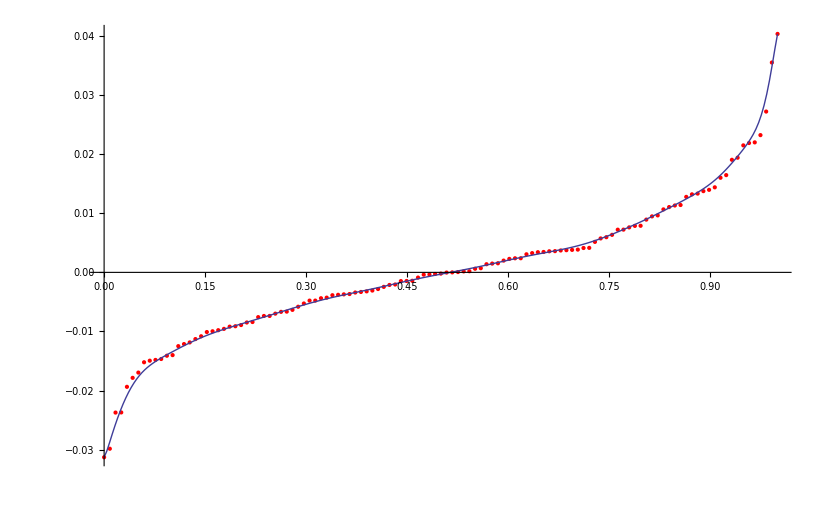

```mathematica
Show[ListPlot[Table[{(i-1)/(Length[hedge]-1),hedge[[i]]},{i,Length[hedge]}],PlotStyle->Red,PlotRange->All],ListPlot[Transpose[Transpose[he][[1;;2]]],Joined->True,PlotRange->All]]
```

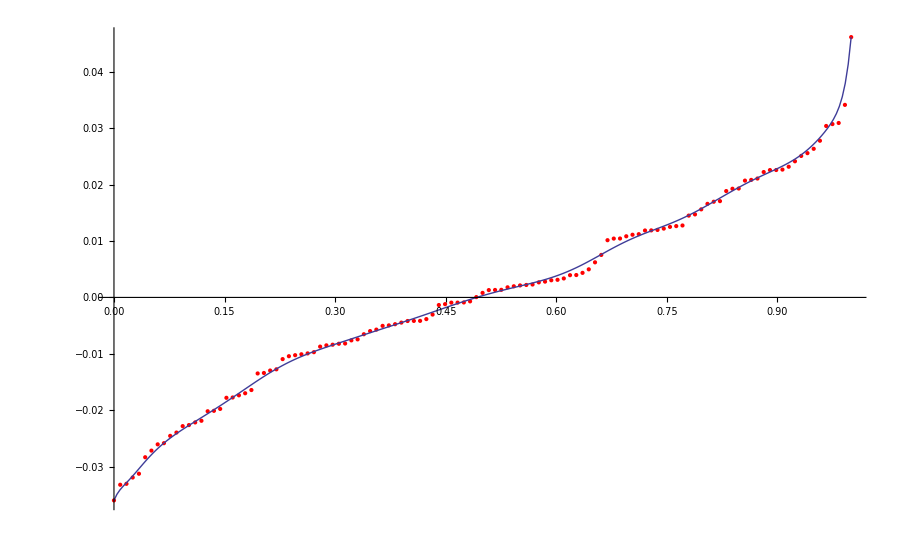

```mathematica
Show[ListPlot[Table[{(i-1)/(Length[dax]-1),Sort[dax][[i]]},{i,Length[dax]}],PlotStyle->Red,PlotRange->All],ListPlot[Transpose[Transpose[da][[1;;2]]],Joined->True,PlotRange->All]]
```

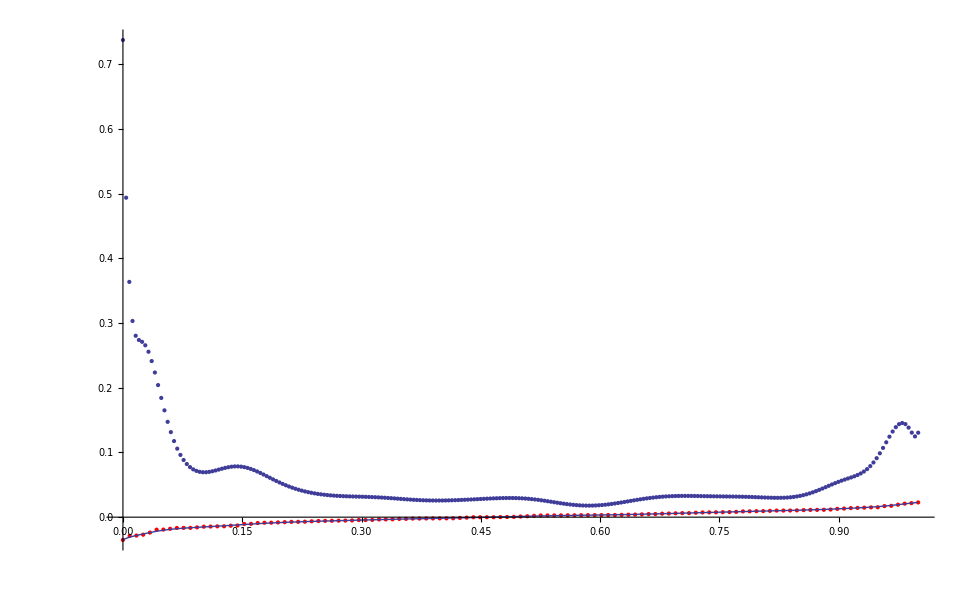

```mathematica
Show[ListPlot[Table[{(i-1)/(Length[d2]-1),Sort[d2][[i]]},{i,Length[d2]}],PlotStyle->Red,PlotRange->All],ListPlot[Transpose[Transpose[da2][[1;;2]]],Joined->True,PlotRange->All],ListPlot[Transpose[{#[[1]],#[[3]]}&[Transpose[da2]]],Joined->False,PlotRange->All]]
```